# Mathematica hw3 complex variables

## 37 iii

### Using integrations to confirm symmetries

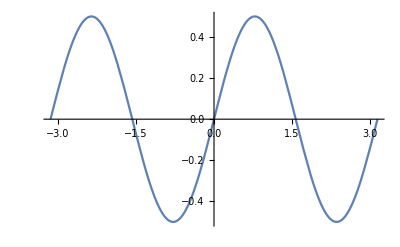

0

```mathematica
Plot[Sin[θ]Cos[θ],{θ,-Pi,Pi}]
Integrate[Sin[θ]Cos[θ],{θ,-Pi,Pi}]
```

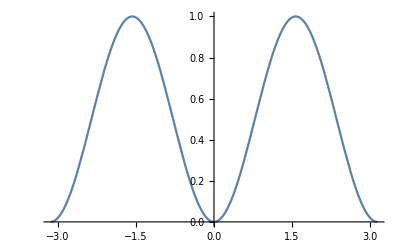

π

```mathematica
Plot[Sin[θ]Sin[θ],{θ,-Pi,Pi}]
Integrate[Sin[θ]Sin[θ],{θ,-Pi,Pi}]
```

### Trying to integrate the infinite series

```mathematica
bn37=Sum[(-1^(n+1)Sin[n*θ])/n,{n,1,Infinity}]
```

-1/2 ⅈ (Log[1-ⅇ^(ⅈ θ)]-Log[ⅇ^(-ⅈ θ) (-1+ⅇ^(ⅈ θ))])

```mathematica
1/Pi*Integrate[Sin[n*θ]bn37,{θ,-Pi,Pi}]
```

(-n π+Sin[n π])/(n^2 π)

## 37 iv

### I get a slightly different plot than the book. Their line passes through 0 while mine jumps at 0. Given that Sin[0] = 0, it should definitely pass through the origin.

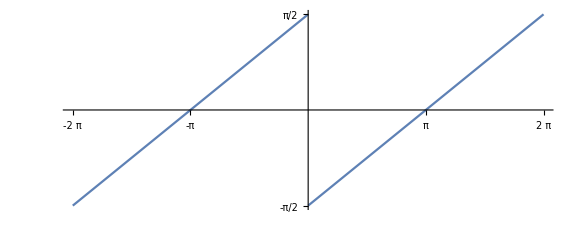

```mathematica
Plot[Sum[-1^(n+1)Sin[n*θ]/n,{n,1,Infinity}],{θ,-2Pi,2Pi},Ticks->{{-2Pi,-Pi,Pi,2Pi},{-Pi/2,Pi/2}},AspectRatio->Automatic,ImageSize->Large]
```

## 38 iv

### Identical plot to the one in the book.

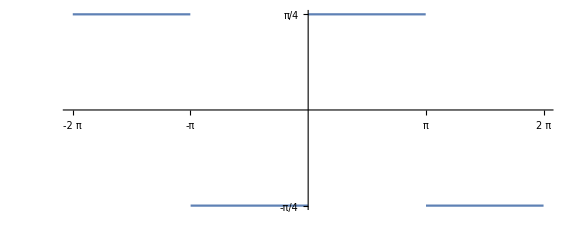

```mathematica
Plot[Sum[Sin[(2*n-1)*θ]/(2*n-1),{n,1,Infinity}],{θ,-2Pi,2Pi},Ticks->{{-2Pi,-Pi,Pi,2Pi},{-Pi/4,Pi/4}},AspectRatio->Automatic,ImageSize->Large]
```

```mathematica
Table[Plot[Sum[Sin[(2*n-1)*θ]/(2*n-1),{n,1,,j}],{θ,-2Pi,2Pi},Ticks->{{-2Pi,-Pi,Pi,2Pi},{-Pi/4,Pi/4}},AspectRatio->Automatic,ImageSize->Large],{j,{1,2}}]
```

$Aborted